```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
ys[x_]:={Cos[2 π x/L],Sin[2 π x /L]}
```

```mathematica
(*check for u[[1]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/ys.csv"][[2;;]];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

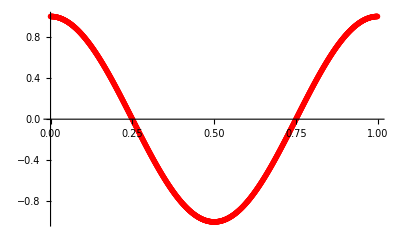

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

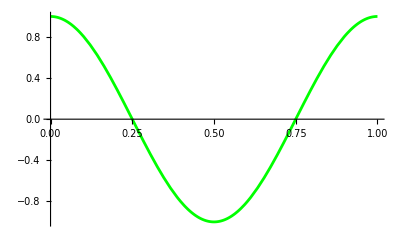

```mathematica
plotexact=Plot[ys[x][[1]],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-ys[t[[i,1]]][[1]]],{i,1,Length[t]}]]
```

3.33067×10^-16

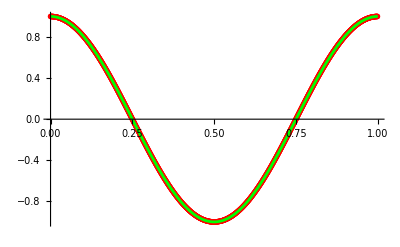

```mathematica
Show[plotnum,plotexact]
```

```mathematica
(*check for u[[2]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/ys.csv"][[2;;]];
t=Table[{t[[i,4]],t[[i,2]]},{i,2,Length[t]}]
```

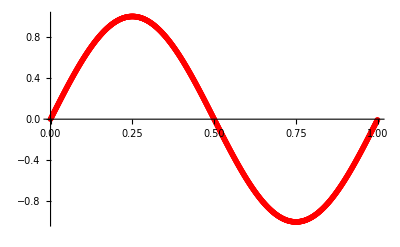

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

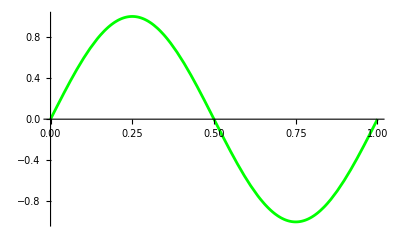

```mathematica
plotexact=Plot[ys[x][[2]],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-ys[t[[i,1]]][[2]]],{i,1,Length[t]}]]
```

1.11022×10^-16

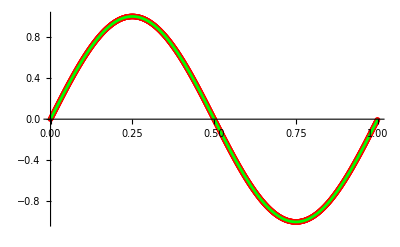

```mathematica
Show[plotnum,plotexact]
```

```mathematica
(*plot normnal*)
```

```mathematica
ys=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/ys.csv"][[2;;]]
u=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/ys.csv"][[2;;]]
```

```mathematica
(*points for the vector field*)
```

```mathematica
X=Table[{ys[[i,1]]+u[[i,1]],ys[[i,2]]+u[[i,2]]},{i,1,Length[u]}]
```

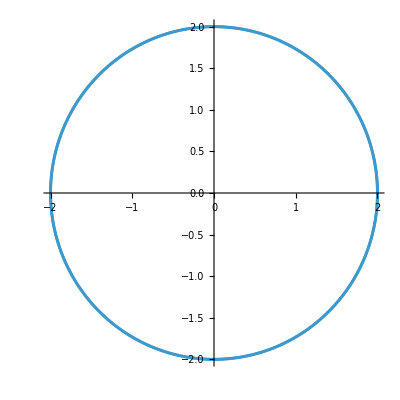

```mathematica
ListPlot[X,AspectRatio->Automatic]
```

```mathematica
(*ListVectorPlot[data]*)
```